Global

```mathematica
Needs["DatabaseLink`"];(*Database library install*)
connection = OpenSQLConnection["mysql"];(*database connect*)
```

```mathematica
data1 = SQLExecute[connection,"Select * from russia_ukraine"];(*quering data from russia_ukraine table*)

data2 = SQLExecute[connection,"Select * from conflict_score"];(*quering data from conflict_score table*)
data2 = Table[{data2[[z]][[2i]],{DateObject[data2[[z]][[1]][[1]]],data2[[z]][[2i+1]]}},{i,Range[15]},{z,1,data2//Length}];(*converting date into date object*)
data2 = Flatten[data2,1];

RusUkr=Table[{DateObject[i[[1,1]]],i[[3]]},{i,data1}];(*formatting data as date-value pair for Russia Ukraine*)
IsrPal = Select[data2,#[[1]]=="Israel-||-Palestine"&][[All,2]];(*formatting data as date-value pair for Israel Palestine*)
ChiUsa = Select[data2,#[[1]]=="China-||-United States"&][[All,2]];(*formatting data as date-value pair for China Usa*)

t1=TimeSeries[RusUkr](*Timeseries creation*)
t2=TimeSeries[IsrPal](*Timeseries creation*)
t3=TimeSeries[ChiUsa](*Timeseries creation*)
```

TimeSeries[…]

TimeSeries[…]

TimeSeries[…]

```mathematica
plotopt={PlotRange->All,PlotLegends->{"Russia-||-Ukraine","Israel-||-Palestine","China-||-United States"},PlotTheme->"Detailed",AspectRatio->0.4,ImageSize->800,ImagePadding->{{30,10},{30,30}},Joined->True};(*Setting plot options for figure plotting*)
```

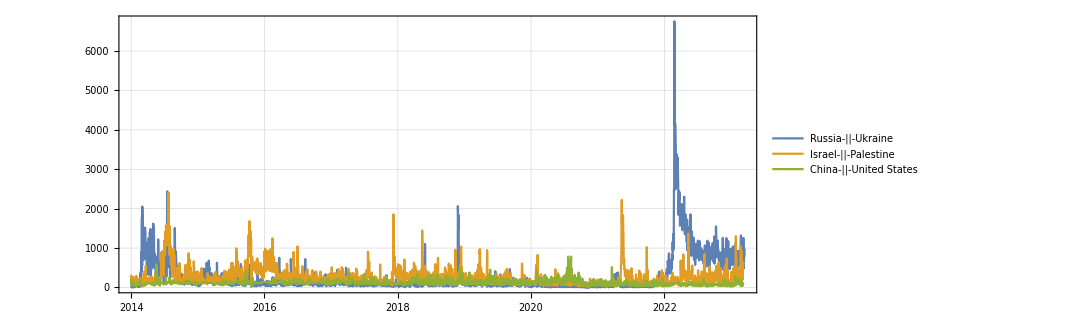

```mathematica
DateListPlot[{t1,t2,t3},PlotLegends->{"Russia-||-Ukraine","Israel-||-Palestine","China-||-United States"},plotopt](* date list plot for all three country pairs*)
```

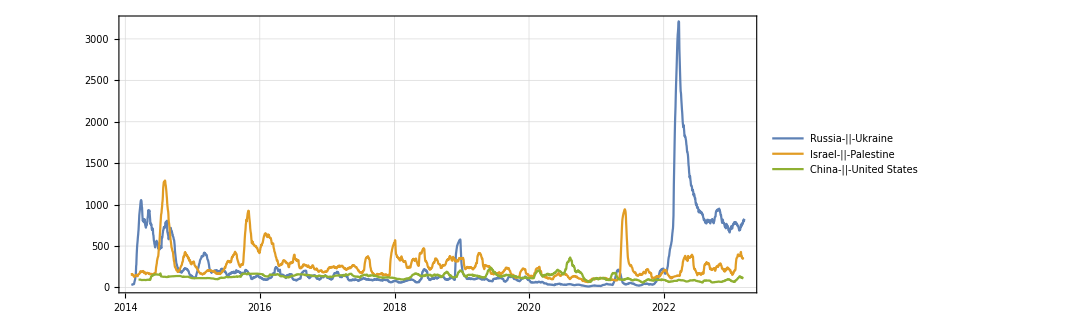

```mathematica
DateListPlot[{MovingAverage[t1,30],MovingAverage[t2,30],MovingAverage[t3,30]},PlotLegends->{"Russia-||-Ukraine","Israel-||-Palestine","China-||-United States"},plotopt](*Moving average date list plot with 30 day lag for all three countries*)
```

Statistical tests (Russia - Ukraine)

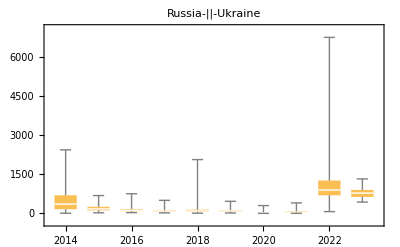

```mathematica
dateset=Table[Select[RusUkr,DateList[#[[1]]][[1]]==i&][[All,2]],{i,2014,2023}];(*creating sets for different year*)
BoxWhiskerChart[dateset,{PlotLabel->"Russia-||-Ukraine",ChartLabels->Range[2014,2023]}](*plotting box-whisker chart*)
```

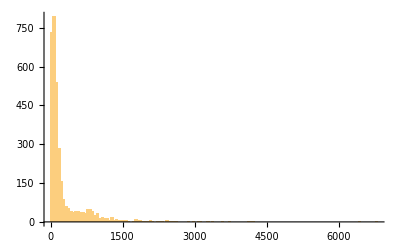

```mathematica
hist=Histogram[RusUkr[[All,2]],Automatic,PlotRange->All](*Histogram plot for all values of russia ukraine timeseries*)
```

```mathematica
dist = FindDistribution[RusUkr[[All,2]]](*Finding best distribution fit*)
```

MixtureDistribution[{0.867858,0.132142},{GeometricDistribution[0.00701692],GeometricDistribution[0.00106871]}]

```mathematica
ShapiroWilkTest[RusUkr[[All,2]],"HypothesisTestData"](*Normal distribution test for Russia Ukraine Timeseries*)
KolmogorovSmirnovTest[RusUkr[[All,2]],NormalDistribution[0,1],"HypothesisTestData"](*Normal distribution test for Russia Ukraine Timeseries*)
DistributionFitTest[RusUkr[[All,2]],NormalDistribution[0,1],"HypothesisTestData"](*Normal distribution test for Russia Ukraine Timeseries*)
```

HypothesisTestData[…]

HypothesisTestData[…]

HypothesisTestData[…]

```mathematica
stationarytest=UnitRootTest[RusUkr[[All,2]],Automatic,"HypothesisTestData"](*Stationarity test for Russia Ukraine Timeseries*)
stationarytest["TestDataTable",All]
stationarytest["TestConclusion"]
```

HypothesisTestData[…]

| Statistic | P-Value
Dickey-Fuller F | -161.484 | 9.69062×10^-11
Dickey-Fuller T | -9.09438 | 5.71355×10^-11
Phillips-Perron F | -84.9573 | 1.79512×10^-8
Phillips-Perron T | -6.67104 | 8.02878×10^-9

The null hypothesis that the model of order 1 without a constant offset and no deterministic trend contains a unit root is rejected at the 5 percent level based on the Dickey-Fuller F test.

```mathematica
autocorrelation = AutocorrelationTest[RusUkr[[All,2]],Automatic,"HypothesisTestData"](*Autocorrelation test for Russia Ukraine Timeseries*)
autocorrelation["TestDataTable",All]
autocorrelation["TestConclusion"]
```

HypothesisTestData[…]

General::munfl: Exp[-10778.7] is too small to represent as a normalized machine number; precision may be lost.

| Statistic | P-Value
Box-Pierce | 5089242781433951611010049270887/235369787792127908194111870 | 0.
Ljung-Box | 11603988581736258465893293652151888679568698015147530923696/535589649552601237116098513853721619020240140307485285 | 0.

The null hypothesis that the data are uncorrelated to lag 9 is rejected at the 5 percent level based on the Ljung-Box test.

Timeseries Decomposition (Russia - Ukraine)

```mathematica
(*Creating module for timeseries decomposition [1]*)decompose[data_,startDate_]:=Module[{dateRange,plot,plotOptions,observedData,observedPlot,trendData,trendPlot,seasonalData,seasonalPlot,randomData,randomPlot,dataDetrended},dateRange={startDate};
(*Setting Plot Options*)plotOptions={PlotRange->All,PlotTheme->"Detailed",AspectRatio->0.2,ImageSize->600,ImagePadding->{{30,10},{15,5}},Joined->True};
(*Observed data*)observedData=TemporalData[data,dateRange]["Path"];
observedPlot=DateListPlot[observedData,Sequence@plotOptions];
(*Extracting trend component*)trendData=Interpolation[MovingAverage[observedData,30],InterpolationOrder->1];
trendPlot=DateListPlot[{#,trendData[#]}&/@observedData[[All,1]],Sequence@plotOptions]//Quiet;
dataDetrended=N@{#[[1]],#[[2]]/trendData[#[[1]]]}&/@observedData//Quiet;
(*Extracting seasonal component*)seasonalData=Mean/@Flatten[Partition[N@dataDetrended[[All,2]],30,30,1],{2}];
seasonalData=TemporalData[PadRight[seasonalData,Length[data],seasonalData],dateRange]["Path"];
seasonalPlot=DateListPlot[seasonalData,Sequence@plotOptions];
(*Extracting random component*)randomData=TimeSeries[dataDetrended[[All,2]]/seasonalData[[All,2]],dateRange]["Path"];
randomPlot=DateListPlot[randomData,Sequence@plotOptions];
(*Plotting data*)plot=Labeled[Grid[Transpose[{Rotate[Style[#,15,Bold],90°]&/@{"observed","trend","seasonality","Noise"},{observedPlot,trendPlot,seasonalPlot,randomPlot}}]],Style["Decomposition of Russia-Ukraine (2014-2023) time series",Bold,17],Top]]
```

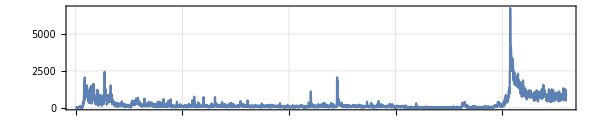
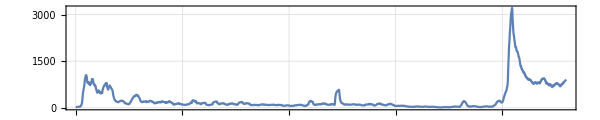
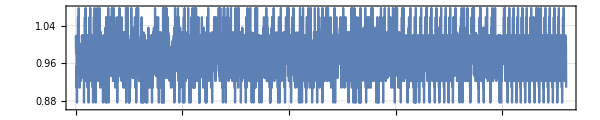
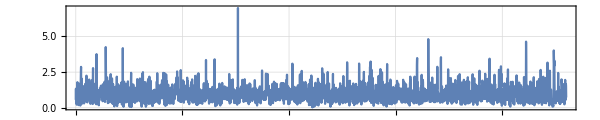
observed | -Graphics-
trend | -Graphics-
seasonality | -Graphics-
Noise | -Graphics-Decomposition of Russia-Ukraine (2014-2023) time series

```mathematica
decompose[RusUkr[[All,2]],RusUkr[[All,1]]]
```

Timeseries Model Fit (Russia Ukraine)

```mathematica
(*Module formation for time series forecast*)
modelfit[timeseries_,modelfamily_]:=Module[{t=timeseries,m=modelfamily},

train=TimeSeriesWindow[t,{DateObject[{2014,1,1}],DateObject[{2021,12,31}]}];(*training series before 2022*)
test=TimeSeriesWindow[t,{DateObject[{2021,12,20}],DateObject[{2023,03,09}]}];(*testing series from 2022 - march 2023*)
traindata = train["Values"];(*training data *)
testdata = test["Values"];(*testing data*)
tmodel=TimeSeriesModelFit[traindata,m];(*fitting timeseries model based on family*)
prediction=Transpose[{test["Dates"],TimeSeriesForecast[tmodel,{testdata//Length}]["Values"]}];(*Predicted values*)
plotopt2={PlotStyle->{Black,Blue,{Dashed,Red}},PlotLabel->tmodel["BestFit"],(*Plot options for datelist plot*)PlotRange->{{DateObject[{2021,1,1}],DateObject[{2023,03,09}]},All},PlotLegends->{"Training values","Testing values","Predicted values"},PlotTheme->"Detailed",AspectRatio->0.4,ImageSize->800,ImagePadding->{{30,10},{30,30}},Joined->True};
predictionimage=DateListPlot[{MovingAverage[train,30],MovingAverage[test,30],prediction},plotopt2];(*moving average filter applied for a clear view*)
residualplot={" ",StyleBox["Residual plot",{"Section",FontColor->Red}]//DisplayForm," ",ListPlot[tmodel["StandardizedResiduals"]["Values"],Filling->Axis,PlotRange->All]}//TableForm;(*Residual plot*)
(*Final set with all important parameters*)
final=Flatten[{predictionimage,residualplot,Table[{" ",StyleBox[i,{"Section",FontColor->Red}]//DisplayForm," ",tmodel[i]},{i,{"ParameterTable","CandidateSelectionTable","ACFPlot","PACFPlot","LjungBoxPlot"}}]},2]//TableForm]
```

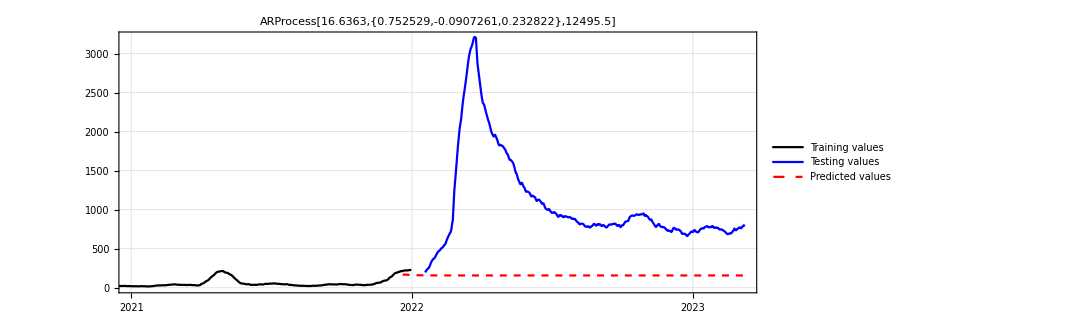
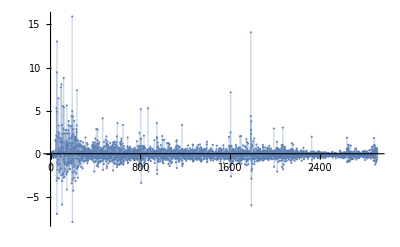
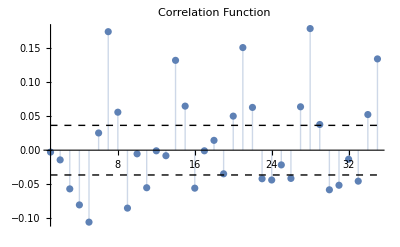
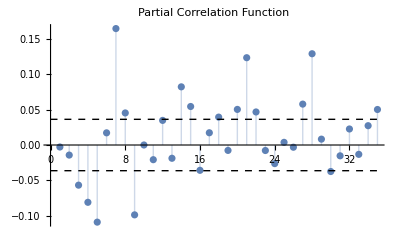
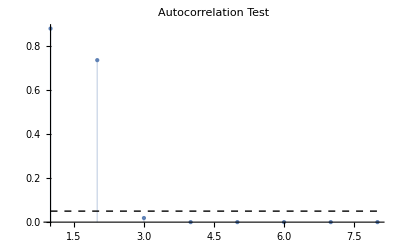
-Graphics-
 
Residual plot
 
-Graphics-
 
ParameterTable
 
 | Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 0.752529 | 0.018022 | 41.7562 | 2.37029×10^-299
𝒶_2 | -0.0907261 | 0.0227252 | -3.99231 | 0.0000335249
𝒶_3 | 0.232822 | 0.018022 | 12.9188 | 1.81455×10^-37
 
CandidateSelectionTable
 
 | Candidate | AIC
1 | ARProcess[3] | 27479.3
2 | ARProcess[4] | 27480.8
3 | ARProcess[2] | 27639.5
 
ACFPlot
 
-Graphics-
 
PACFPlot
 
-Graphics-
 
LjungBoxPlot
 
-Graphics-

```mathematica
modelfit[t1,"AR"](*Timeseries model fit of family AR *)
```

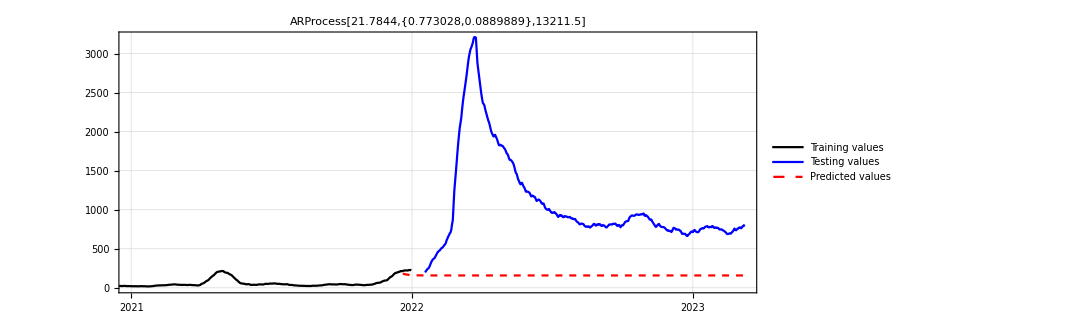
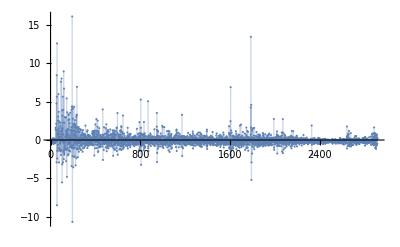
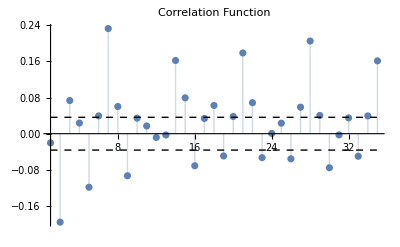
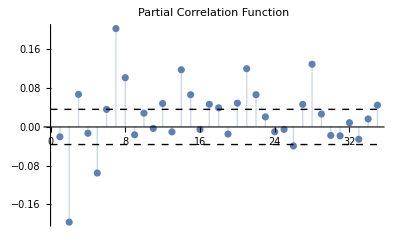
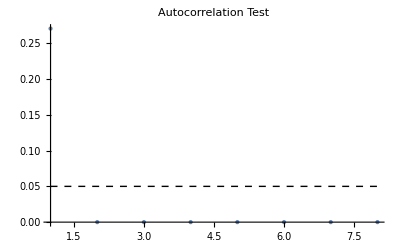
-Graphics-
 
Residual plot
 
-Graphics-
 
ParameterTable
 
 | Estimate | Standard Error | t-Statistic | P-Value
𝒶_1 | 0.773028 | 0.0184577 | 41.881 | 9.05887×10^-301
𝒶_2 | 0.0889889 | 0.0184577 | 4.82123 | 7.49992×10^-7
 
CandidateSelectionTable
 
 | Candidate | AIC
1 | ARProcess[2] | 27639.5
2 | ARProcess[2] | 27654.4
3 | ARProcess[1] | 27660.8
4 | ARProcess[1] | 27660.9
5 | ARMAProcess[2,1] | 27663.9
6 | ARMAProcess[2,1] | 27679.3
7 | ARMAProcess[1,1] | 27733.8
8 | MAProcess[1] | 29620.3
9 | MAProcess[0] | 31377.2
10 | MAProcess[0] | 31377.2
 
ACFPlot
 
-Graphics-
 
PACFPlot
 
-Graphics-
 
LjungBoxPlot
 
-Graphics-

```mathematica
modelfit[t1,"SARIMA"](*Timeseries model fit of family SARIMA *)
```

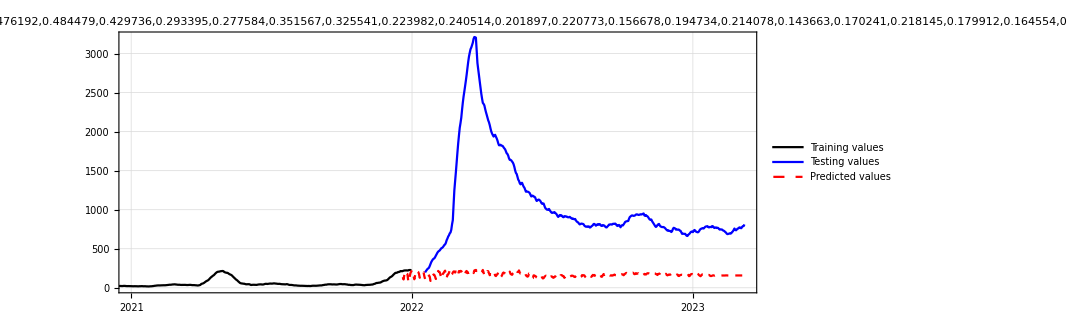
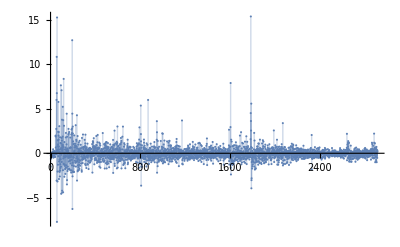
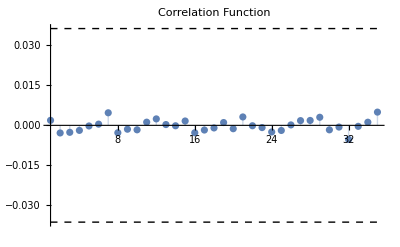
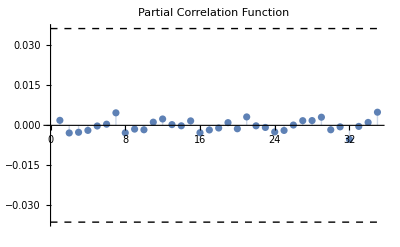
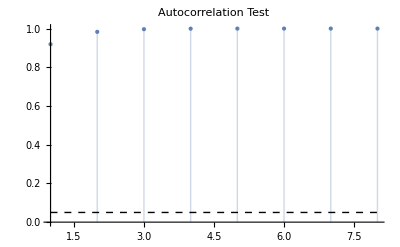
-Graphics-
 
Residual plot
 
-Graphics-
 
ParameterTable
 
 | Estimate | Standard Error | t-Statistic | P-Value
𝒷_1 | 0.712987 | 0.0185245 | 38.4888 | 1.12551×10^-262
𝒷_2 | 0.476192 | 0.0227486 | 20.9328 | 4.70339×10^-91
𝒷_3 | 0.484479 | 0.0243999 | 19.8558 | 1.09374×10^-82
𝒷_4 | 0.429736 | 0.0259989 | 16.529 | 4.94959×10^-59
𝒷_5 | 0.293395 | 0.0271909 | 10.7902 | 6.06808×10^-27
𝒷_6 | 0.277584 | 0.0277292 | 10.0105 | 1.61843×10^-23
𝒷_7 | 0.351567 | 0.0282007 | 12.4666 | 4.31835×10^-35
𝒷_8 | 0.325541 | 0.028941 | 11.2484 | 4.57957×10^-29
𝒷_9 | 0.223982 | 0.0295509 | 7.57952 | 2.31607×10^-14
𝒷_10 | 0.240514 | 0.0298352 | 8.06141 | 5.4496×10^-16
𝒷_11 | 0.201897 | 0.030166 | 6.69286 | 1.30759×10^-11
𝒷_12 | 0.220773 | 0.0303955 | 7.26335 | 2.41222×10^-13
𝒷_13 | 0.156678 | 0.0306689 | 5.10871 | 1.72648×10^-7
𝒷_14 | 0.194734 | 0.030806 | 6.32131 | 1.49546×10^-10
𝒷_15 | 0.214078 | 0.031009 | 6.90376 | 3.09582×10^-12
𝒷_16 | 0.143663 | 0.0312568 | 4.59622 | 2.24267×10^-6
𝒷_17 | 0.170241 | 0.031368 | 5.42722 | 3.09709×10^-8
𝒷_18 | 0.218145 | 0.0315262 | 6.91947 | 2.77613×10^-12
𝒷_19 | 0.179912 | 0.0317843 | 5.6604 | 8.28596×10^-9
𝒷_20 | 0.164554 | 0.0319569 | 5.14925 | 1.39474×10^-7
𝒷_21 | 0.222856 | 0.0321021 | 6.94211 | 2.37177×10^-12
𝒷_22 | 0.215366 | 0.0323637 | 6.65456 | 1.69097×10^-11
𝒷_23 | 0.160427 | 0.0325953 | 4.92178 | 4.52667×10^-7
𝒷_24 | 0.142363 | 0.0327242 | 4.35038 | 7.02858×10^-6
𝒷_25 | 0.13675 | 0.0328283 | 4.16562 | 0.0000159765
𝒷_26 | 0.108254 | 0.0329257 | 3.28781 | 0.00051084
𝒷_27 | 0.141797 | 0.032985 | 4.29884 | 8.86647×10^-6
𝒷_28 | 0.233305 | 0.0330892 | 7.0508 | 1.10634×10^-12
𝒷_29 | 0.186528 | 0.0333703 | 5.58963 | 1.24305×10^-8
𝒷_30 | 0.109344 | 0.0335439 | 3.25973 | 0.000564015
𝒷_31 | 0.0975338 | 0.0336049 | 2.90237 | 0.00186568
𝒷_32 | 0.11945 | 0.0336523 | 3.54955 | 0.000195999
𝒷_33 | 0.0832881 | 0.0337239 | 2.4697 | 0.00678973
𝒷_34 | 0.0983779 | 0.0337592 | 2.91411 | 0.00179713
𝒷_35 | 0.146482 | 0.0338084 | 4.33273 | 7.61289×10^-6
𝒷_36 | 0.155444 | 0.0339171 | 4.58306 | 2.38748×10^-6
𝒷_37 | 0.0904013 | 0.0340361 | 2.65605 | 0.0039747
𝒷_38 | 0.0290218 | 0.034075 | 0.851702 | 0.197225
𝒷_39 | 0.090998 | 0.0340768 | 2.67038 | 0.00380929
𝒷_40 | 0.124371 | 0.0341176 | 3.64536 | 0.000135843
𝒷_41 | 0.0829477 | 0.0341953 | 2.42571 | 0.00766949
𝒷_42 | 0.210507 | 0.0342296 | 6.14986 | 4.40764×10^-10
𝒷_43 | 0.223115 | 0.0344484 | 6.4768 | 5.4793×10^-11
𝒷_44 | 0.183945 | 0.0346874 | 5.30294 | 6.12425×10^-8
𝒷_45 | 0.151325 | 0.0348534 | 4.34176 | 7.30852×10^-6
𝒷_46 | 0.157094 | 0.0349647 | 4.49294 | 3.64918×10^-6
𝒷_47 | 0.126723 | 0.0350843 | 3.61196 | 0.000154513
𝒷_48 | 0.0687581 | 0.0351566 | 1.95576 | 0.0252943
𝒷_49 | 0.177806 | 0.035179 | 5.05431 | 2.29326×10^-7
𝒷_50 | 0.21665 | 0.0353291 | 6.13234 | 4.91487×10^-10
𝒷_51 | 0.163911 | 0.0355486 | 4.61089 | 2.09115×10^-6
𝒷_52 | 0.128087 | 0.0356776 | 3.59012 | 0.000167992
𝒷_53 | 0.140781 | 0.0357562 | 3.93724 | 0.0000421776
𝒷_54 | 0.101278 | 0.0358433 | 2.82557 | 0.00237594
𝒷_55 | 0.0460685 | 0.0358818 | 1.28389 | 0.0996408
𝒷_56 | 0.142806 | 0.035885 | 3.97955 | 0.0000353655
𝒷_57 | 0.133671 | 0.0359681 | 3.71637 | 0.000102955
𝒷_58 | 0.0655593 | 0.0360357 | 1.81929 | 0.0344851
𝒷_59 | 0.0721156 | 0.0360395 | 2.00101 | 0.0227418
𝒷_60 | 0.0383342 | 0.0360596 | 1.06308 | 0.143917
𝒷_61 | 0.0610157 | 0.0360646 | 1.69184 | 0.0453915
𝒷_62 | 0.111514 | 0.0360696 | 3.09163 | 0.00100472
𝒷_63 | 0.0858848 | 0.0361217 | 2.37765 | 0.00874382
𝒷_64 | 0.0998377 | 0.0361537 | 2.76148 | 0.00289503
𝒷_65 | 0.0937194 | 0.0361816 | 2.59025 | 0.00481922
𝒷_66 | 0.0900178 | 0.0362084 | 2.4861 | 0.00648543
𝒷_67 | 0.0667168 | 0.0362424 | 1.84085 | 0.0328727
𝒷_68 | 0.0488797 | 0.0362632 | 1.34791 | 0.0888955
𝒷_69 | 0.0604331 | 0.0362656 | 1.66641 | 0.0478701
𝒷_70 | 0.0914286 | 0.0362753 | 2.52041 | 0.0058875
𝒷_71 | 0.0829595 | 0.0363037 | 2.28515 | 0.0111878
𝒷_72 | 0.0661057 | 0.036319 | 1.82014 | 0.0344199
𝒷_73 | 0.0738564 | 0.0363323 | 2.0328 | 0.0210815
𝒷_74 | 0.0906376 | 0.0363541 | 2.49319 | 0.00635764
𝒷_75 | 0.0420403 | 0.0363924 | 1.1552 | 0.124053
𝒷_76 | 0.0852064 | 0.0363995 | 2.34087 | 0.00965309
𝒷_77 | 0.131627 | 0.0364315 | 3.613 | 0.000153894
𝒷_78 | 0.110917 | 0.0365073 | 3.03823 | 0.00120044
𝒷_79 | 0.105187 | 0.0365528 | 2.87769 | 0.00201759
𝒷_80 | 0.0970056 | 0.0366002 | 2.65041 | 0.00404143
𝒷_81 | 0.0446414 | 0.0366387 | 1.21842 | 0.111581
𝒷_82 | 0.0246318 | 0.0366441 | 0.672189 | 0.250758
𝒷_83 | -0.00348822 | 0.0366392 | -0.0952045 | 0.462079
𝒷_84 | 0.120996 | 0.0366319 | 3.30303 | 0.000484015
𝒷_85 | 0.139058 | 0.0366941 | 3.78966 | 0.000076954
𝒷_86 | 0.101444 | 0.0367792 | 2.75818 | 0.0029244
𝒷_87 | 0.0477217 | 0.0368247 | 1.29592 | 0.0975535
𝒷_88 | 0.0727328 | 0.0368346 | 1.97458 | 0.0242053
𝒷_89 | 0.0640339 | 0.0368587 | 1.73728 | 0.0412219
𝒷_90 | 0.0116091 | 0.0368761 | 0.314813 | 0.376463
𝒷_91 | 0.117632 | 0.0368696 | 3.19048 | 0.000717734
𝒷_92 | 0.147322 | 0.0369236 | 3.98992 | 0.000033862
𝒷_93 | 0.0918843 | 0.037008 | 2.48282 | 0.00654525
𝒷_94 | 0.0722442 | 0.0370382 | 1.95053 | 0.0256043
𝒷_95 | 0.137992 | 0.0370612 | 3.72336 | 0.000100155
𝒷_96 | 0.0826187 | 0.0371478 | 2.22405 | 0.0131106
𝒷_97 | 0.0766886 | 0.037174 | 2.06296 | 0.0196023
𝒷_98 | 0.08061 | 0.0371978 | 2.16706 | 0.0151554
𝒷_99 | 0.0678 | 0.0372222 | 1.82149 | 0.0343173
𝒷_100 | 0.0397667 | 0.0372217 | 1.06837 | 0.14272
𝒷_101 | 0.0749405 | 0.037217 | 2.01361 | 0.0220712
𝒷_102 | 0.121014 | 0.0372405 | 3.24952 | 0.000584567
𝒷_103 | 0.0366279 | 0.0373064 | 0.981812 | 0.163137
𝒷_104 | 0.0470924 | 0.0373121 | 1.26212 | 0.103503
𝒷_105 | 0.100236 | 0.0373179 | 2.68602 | 0.00363598
𝒷_106 | 0.0725989 | 0.0373599 | 1.94323 | 0.0260422
𝒷_107 | 0.0579429 | 0.0373789 | 1.55015 | 0.0606074
𝒷_108 | 0.0623475 | 0.0373926 | 1.66737 | 0.0477737
𝒷_109 | 0.0812002 | 0.0374098 | 2.17056 | 0.0150226
𝒷_110 | 0.00459891 | 0.0374401 | 0.122834 | 0.451123
𝒷_111 | -0.0051825 | 0.0374396 | -0.138423 | 0.444958
𝒷_112 | 0.06017 | 0.0374336 | 1.60738 | 0.0540398
𝒷_113 | 0.071104 | 0.0374475 | 1.89877 | 0.0288469
𝒷_114 | 0.0422308 | 0.0374675 | 1.12713 | 0.12989
𝒷_115 | 0.0743415 | 0.0374755 | 1.98374 | 0.0236895
𝒷_116 | 0.0756104 | 0.0375004 | 2.01625 | 0.0219326
𝒷_117 | 0.0516205 | 0.0375266 | 1.37557 | 0.0845299
𝒷_118 | 0.0402982 | 0.0375328 | 1.07368 | 0.141528
𝒷_119 | 0.0946458 | 0.0375331 | 2.52166 | 0.00586654
𝒷_120 | 0.121075 | 0.0375715 | 3.22253 | 0.000642325
𝒷_121 | 0.102744 | 0.037632 | 2.73023 | 0.00318359
𝒷_122 | 0.121648 | 0.0376801 | 3.22844 | 0.000629246
𝒷_123 | 0.13295 | 0.0377472 | 3.52212 | 0.000217345
𝒷_124 | 0.0946169 | 0.0378272 | 2.5013 | 0.00621423
𝒷_125 | 0.0642032 | 0.0378677 | 1.69546 | 0.0450476
𝒷_126 | 0.117704 | 0.0378857 | 3.10683 | 0.000954637
𝒷_127 | 0.101254 | 0.0379484 | 2.66821 | 0.00383402
𝒷_128 | 0.0760358 | 0.0379938 | 2.00127 | 0.0227279
𝒷_129 | 0.0878869 | 0.0380188 | 2.31167 | 0.0104326
𝒷_130 | 0.0523281 | 0.0380534 | 1.37512 | 0.0845998
𝒷_131 | 0.0211225 | 0.0380629 | 0.554938 | 0.28949
𝒷_132 | 0.0494755 | 0.0380643 | 1.29979 | 0.0968886
𝒷_133 | 0.0877021 | 0.0380753 | 2.30338 | 0.0106637
𝒷_134 | 0.113415 | 0.0381099 | 2.976 | 0.00147219
𝒷_135 | 0.150122 | 0.0381639 | 3.9336 | 0.0000428188
𝒷_136 | 0.093519 | 0.038263 | 2.44411 | 0.00729001
𝒷_137 | 0.0931092 | 0.038298 | 2.43118 | 0.00755492
𝒷_138 | 0.12651 | 0.0383348 | 3.30012 | 0.000489036
𝒷_139 | 0.0870574 | 0.0384014 | 2.26704 | 0.0117304
𝒷_140 | 0.105911 | 0.0384347 | 2.7556 | 0.00294747
𝒷_141 | 0.155992 | 0.0384842 | 4.0534 | 0.0000259001
𝒷_142 | 0.115073 | 0.0385879 | 2.9821 | 0.00144328
𝒷_143 | 0.15552 | 0.0386436 | 4.02446 | 0.0000292808
𝒷_144 | 0.090323 | 0.038751 | 2.33086 | 0.00991438
𝒷_145 | 0.0915007 | 0.0387871 | 2.35905 | 0.0091937
𝒷_146 | 0.0937737 | 0.038824 | 2.41535 | 0.00789057
𝒷_147 | 0.0953654 | 0.0388604 | 2.45405 | 0.00709196
𝒷_148 | 0.137966 | 0.0388994 | 3.54675 | 0.000198081
𝒷_149 | 0.0987781 | 0.0389781 | 2.5342 | 0.00566123
𝒷_150 | 0.0940537 | 0.0390141 | 2.41076 | 0.00799048
𝒷_151 | 0.0743874 | 0.0390517 | 1.90485 | 0.0284492
𝒷_152 | 0.0229032 | 0.039075 | 0.586134 | 0.278915
𝒷_153 | 0.0164768 | 0.0390766 | 0.421653 | 0.336655
𝒷_154 | 0.0590866 | 0.0390775 | 1.51204 | 0.0653164
𝒷_155 | 0.0792125 | 0.0390891 | 2.02646 | 0.0214043
𝒷_156 | 0.0485904 | 0.0391143 | 1.24227 | 0.107119
𝒷_157 | 0.0364362 | 0.0391241 | 0.931298 | 0.175888
𝒷_158 | 0.0567293 | 0.0391297 | 1.44978 | 0.0736143
𝒷_159 | 0.0458557 | 0.0391436 | 1.17147 | 0.120752
𝒷_160 | 0.0447755 | 0.0391528 | 1.14361 | 0.12644
𝒷_161 | 0.0816452 | 0.0391612 | 2.08485 | 0.0185849
𝒷_162 | 0.0751093 | 0.0391886 | 1.91661 | 0.0276927
𝒷_163 | 0.0762967 | 0.0392113 | 1.94579 | 0.0258883
𝒷_164 | 0.0781803 | 0.0392362 | 1.99256 | 0.0232017
𝒷_165 | 0.0729252 | 0.0392618 | 1.85741 | 0.031677
𝒷_166 | 0.0674699 | 0.0392838 | 1.7175 | 0.0429969
𝒷_167 | 0.0447916 | 0.0393025 | 1.13966 | 0.127261
𝒷_168 | 0.0644098 | 0.0393111 | 1.63846 | 0.0507167
𝒷_169 | 0.0681637 | 0.0393287 | 1.73318 | 0.0415847
𝒷_170 | 0.0554074 | 0.039346 | 1.40821 | 0.0795878
𝒷_171 | 0.0504913 | 0.0393583 | 1.28286 | 0.0998209
𝒷_172 | 0.0121989 | 0.0393691 | 0.30986 | 0.378345
𝒷_173 | 0.02624 | 0.0393695 | 0.666506 | 0.25257
𝒷_174 | 0.0447736 | 0.0393711 | 1.13722 | 0.12777
𝒷_175 | 0.0717325 | 0.0393776 | 1.82166 | 0.0343048
𝒷_176 | 0.0572331 | 0.0393972 | 1.45272 | 0.0732045
𝒷_177 | 0.0772964 | 0.0394062 | 1.96153 | 0.0249563
𝒷_178 | 0.0434805 | 0.0394317 | 1.10268 | 0.135129
𝒷_179 | 0.0777509 | 0.0394399 | 1.97137 | 0.0243878
𝒷_180 | 0.13155 | 0.0394662 | 3.33322 | 0.000434604
𝒷_181 | 0.115912 | 0.0395412 | 2.93141 | 0.00170027
𝒷_182 | 0.134479 | 0.039599 | 3.39602 | 0.000346445
𝒷_183 | 0.119795 | 0.0396765 | 3.0193 | 0.00127778
𝒷_184 | 0.107637 | 0.0397356 | 2.70884 | 0.00339571
𝒷_185 | 0.102826 | 0.0397852 | 2.58453 | 0.00489965
𝒷_186 | 0.0898662 | 0.0398308 | 2.2562 | 0.0120661
𝒷_187 | 0.0849113 | 0.0398653 | 2.12995 | 0.0166295
𝒷_188 | 0.0668217 | 0.0398956 | 1.67492 | 0.0470289
𝒷_189 | 0.101103 | 0.0399143 | 2.533 | 0.00568052
𝒷_190 | 0.085992 | 0.0399582 | 2.15205 | 0.0157378
𝒷_191 | 0.0622491 | 0.0399856 | 1.55679 | 0.0598149
𝒷_192 | 0.0323411 | 0.0400013 | 0.808502 | 0.209434
𝒷_193 | 0.0247115 | 0.0400058 | 0.617699 | 0.268411
𝒷_194 | 0.04397 | 0.0400063 | 1.09908 | 0.135913
𝒷_195 | 0.0645436 | 0.0400124 | 1.61309 | 0.0534163
𝒷_196 | 0.075179 | 0.0400302 | 1.87806 | 0.0302364
𝒷_197 | 0.053135 | 0.0400494 | 1.32674 | 0.09235
𝒷_198 | 0.0489487 | 0.0400575 | 1.22196 | 0.110911
𝒷_199 | 0.019265 | 0.0400677 | 0.48081 | 0.315344
𝒷_200 | -0.000356027 | 0.0400692 | -0.0088853 | 0.496456
𝒷_201 | 0.0325846 | 0.0400691 | 0.813211 | 0.208082
𝒷_202 | 0.0350305 | 0.0400736 | 0.874153 | 0.191054
𝒷_203 | 0.0366623 | 0.0400787 | 0.914756 | 0.180198
𝒷_204 | 0.0276306 | 0.0400829 | 0.689335 | 0.245334
𝒷_205 | 0.0381363 | 0.0400829 | 0.951435 | 0.170731
𝒷_206 | 0.0347385 | 0.0400866 | 0.866585 | 0.19312
𝒷_207 | 0.0106802 | 0.0400914 | 0.266397 | 0.394976
𝒷_208 | 0.0185131 | 0.0400916 | 0.461769 | 0.322141
𝒷_209 | 0.021966 | 0.0400921 | 0.54789 | 0.291905
𝒷_210 | 0.0474126 | 0.0400906 | 1.18264 | 0.118525
𝒷_211 | 0.0519946 | 0.0400887 | 1.29699 | 0.0973685
𝒷_212 | 0.028647 | 0.0400906 | 0.714556 | 0.23747
𝒷_213 | 0.0153538 | 0.0400921 | 0.382963 | 0.350888
𝒷_214 | 0.00808407 | 0.0400916 | 0.20164 | 0.420106
𝒷_215 | 0.00967277 | 0.0400914 | 0.241268 | 0.404682
𝒷_216 | 0.0243511 | 0.0400866 | 0.607463 | 0.271796
𝒷_217 | 0.0275623 | 0.0400829 | 0.687633 | 0.245869
𝒷_218 | 0.019165 | 0.0400829 | 0.478134 | 0.316295
𝒷_219 | 0.00561635 | 0.0400787 | 0.140133 | 0.444282
𝒷_220 | 0.0015892 | 0.0400736 | 0.0396571 | 0.484185
𝒷_221 | -0.00501377 | 0.0400691 | -0.125128 | 0.450215
𝒷_222 | 0.00581485 | 0.0400692 | 0.14512 | 0.442313
𝒷_223 | -0.00304676 | 0.0400677 | -0.0760403 | 0.469696
𝒷_224 | 0.0305284 | 0.0400575 | 0.762114 | 0.223027
𝒷_225 | 0.0341442 | 0.0400494 | 0.852553 | 0.196989
𝒷_226 | 0.00402544 | 0.0400302 | 0.10056 | 0.459953
𝒷_227 | 0.0229518 | 0.0400124 | 0.573617 | 0.283136
𝒷_228 | 0.0220815 | 0.0400063 | 0.55195 | 0.290512
𝒷_229 | -0.00153779 | 0.0400058 | -0.0384392 | 0.48467
𝒷_230 | 0.0147788 | 0.0400013 | 0.369458 | 0.355907
𝒷_231 | 0.0319528 | 0.0399856 | 0.799109 | 0.212146
𝒷_232 | -0.00278505 | 0.0399582 | -0.069699 | 0.472219
𝒷_233 | 0.0102419 | 0.0399143 | 0.256597 | 0.398754
𝒷_234 | 0.0136041 | 0.0398956 | 0.340993 | 0.366567
𝒷_235 | 0.00833066 | 0.0398653 | 0.20897 | 0.417243
𝒷_236 | 0.0017588 | 0.0398308 | 0.0441567 | 0.482391
𝒷_237 | 0.0102451 | 0.0397852 | 0.257511 | 0.398401
𝒷_238 | 0.0261437 | 0.0397356 | 0.657941 | 0.255314
𝒷_239 | 0.0137029 | 0.0396765 | 0.345365 | 0.364922
𝒷_240 | 0.0110534 | 0.039599 | 0.279133 | 0.390081
𝒷_241 | 0.00687826 | 0.0395412 | 0.173951 | 0.430958
𝒷_242 | -0.0022943 | 0.0394662 | -0.0581332 | 0.476823
𝒷_243 | -0.000632705 | 0.0394399 | -0.0160423 | 0.493601
𝒷_244 | 0.0112598 | 0.0394317 | 0.285552 | 0.387621
𝒷_245 | 0.0346241 | 0.0394062 | 0.878646 | 0.189833
𝒷_246 | 0.0256459 | 0.0393972 | 0.650959 | 0.257562
𝒷_247 | 0.0227164 | 0.0393776 | 0.576887 | 0.28203
𝒷_248 | 0.0178138 | 0.0393711 | 0.452459 | 0.325486
𝒷_249 | 0.00767405 | 0.0393695 | 0.194924 | 0.422733
𝒷_250 | 0.00767969 | 0.0393691 | 0.195069 | 0.422676
𝒷_251 | 0.0158581 | 0.0393583 | 0.402916 | 0.34352
𝒷_252 | 0.0262406 | 0.039346 | 0.666921 | 0.252438
𝒷_253 | 0.0114015 | 0.0393287 | 0.289903 | 0.385956
𝒷_254 | 0.00599906 | 0.0393111 | 0.152605 | 0.43936
𝒷_255 | 0.0159799 | 0.0393025 | 0.406587 | 0.34217
𝒷_256 | 0.0171958 | 0.0392838 | 0.437734 | 0.330806
𝒷_257 | 0.0160495 | 0.0392618 | 0.408781 | 0.341365
𝒷_258 | 0.0114335 | 0.0392362 | 0.291403 | 0.385382
𝒷_259 | 0.0217817 | 0.0392113 | 0.555496 | 0.289299
𝒷_260 | 0.0201495 | 0.0391886 | 0.514166 | 0.303588
𝒷_261 | 0.00970623 | 0.0391612 | 0.247853 | 0.402133
𝒷_262 | 0.00192001 | 0.0391528 | 0.0490389 | 0.480446
𝒷_263 | -0.0061836 | 0.0391436 | -0.157972 | 0.437245
𝒷_264 | 0.00754388 | 0.0391297 | 0.192792 | 0.423568
𝒷_265 | 0.0117966 | 0.0391241 | 0.301517 | 0.381521
𝒷_266 | 0.023063 | 0.0391143 | 0.58963 | 0.277742
𝒷_267 | 0.0289759 | 0.0390891 | 0.741279 | 0.229292
𝒷_268 | 0.00888077 | 0.0390775 | 0.227261 | 0.410118
𝒷_269 | -0.0125245 | 0.0390766 | -0.320512 | 0.374301
𝒷_270 | -0.0149426 | 0.039075 | -0.382409 | 0.351093
𝒷_271 | -0.0177102 | 0.0390517 | -0.453507 | 0.325109
𝒷_272 | 0.0395234 | 0.0390141 | 1.01305 | 0.155559
𝒷_273 | 0.0344647 | 0.0389781 | 0.884207 | 0.188329
𝒷_274 | 0.0166425 | 0.0388994 | 0.427836 | 0.334401
𝒷_275 | 0.0235165 | 0.0388604 | 0.605153 | 0.272562
𝒷_276 | 0.00562049 | 0.038824 | 0.144769 | 0.442452
𝒷_277 | -0.000919019 | 0.0387871 | -0.0236939 | 0.490549
𝒷_278 | -0.0016074 | 0.038751 | -0.0414802 | 0.483458
𝒷_279 | 0.0266458 | 0.0386436 | 0.689527 | 0.245273
𝒷_280 | 0.0323371 | 0.0385879 | 0.83801 | 0.201047
𝒷_281 | 0.0119908 | 0.0384842 | 0.311578 | 0.377692
𝒷_282 | 0.0108698 | 0.0384347 | 0.282813 | 0.38867
𝒷_283 | 0.0337053 | 0.0384014 | 0.877711 | 0.190086
𝒷_284 | 0.0211174 | 0.0383348 | 0.550866 | 0.290884
𝒷_285 | 0.0308607 | 0.038298 | 0.805805 | 0.21021
𝒷_286 | 0.0219212 | 0.038263 | 0.572908 | 0.283376
𝒷_287 | 0.0292685 | 0.0381639 | 0.766916 | 0.221597
𝒷_288 | 0.00549356 | 0.0381099 | 0.144151 | 0.442696
𝒷_289 | 0.00240127 | 0.0380753 | 0.0630662 | 0.474859
𝒷_290 | 0.0109571 | 0.0380643 | 0.287856 | 0.386739
𝒷_291 | 0.025486 | 0.0380629 | 0.669576 | 0.251591
𝒷_292 | 0.00643999 | 0.0380534 | 0.169235 | 0.432812
𝒷_293 | 0.0157958 | 0.0380188 | 0.415473 | 0.338913
𝒷_294 | 0.0146543 | 0.0379938 | 0.385703 | 0.349872
𝒷_295 | 0.00389317 | 0.0379484 | 0.102591 | 0.459147
𝒷_296 | -0.0123767 | 0.0378857 | -0.326685 | 0.371965
𝒷_297 | -0.00364657 | 0.0378677 | -0.0962977 | 0.461645
𝒷_298 | -0.008428 | 0.0378272 | -0.222803 | 0.411852
𝒷_299 | -0.00826094 | 0.0377472 | -0.218849 | 0.413391
𝒷_300 | 0.00399016 | 0.0376801 | 0.105896 | 0.457836
𝒷_301 | 0.037355 | 0.037632 | 0.992638 | 0.160484
𝒷_302 | 0.0237415 | 0.0375715 | 0.631903 | 0.26375
𝒷_303 | 0.0396169 | 0.0375331 | 1.05552 | 0.145638
𝒷_304 | 0.0359526 | 0.0375328 | 0.957898 | 0.169097
𝒷_305 | 0.00299608 | 0.0375266 | 0.0798389 | 0.468185
𝒷_306 | -0.00909804 | 0.0375004 | -0.242612 | 0.404162
𝒷_307 | 0.00662246 | 0.0374755 | 0.176714 | 0.429873
𝒷_308 | 0.0260017 | 0.0374675 | 0.69398 | 0.243875
𝒷_309 | 0.0245724 | 0.0374475 | 0.656185 | 0.255879
𝒷_310 | 0.0363388 | 0.0374336 | 0.970754 | 0.165876
𝒷_311 | 0.0114969 | 0.0374396 | 0.307079 | 0.379403
𝒷_312 | 0.000928749 | 0.0374401 | 0.0248063 | 0.490106
𝒷_313 | 0.0118438 | 0.0374098 | 0.316596 | 0.375786
𝒷_314 | 0.0195486 | 0.0373926 | 0.522793 | 0.300579
𝒷_315 | 0.0334366 | 0.0373789 | 0.89453 | 0.185556
𝒷_316 | 0.0302439 | 0.0373599 | 0.80953 | 0.209138
𝒷_317 | 0.0311731 | 0.0373179 | 0.835339 | 0.201798
𝒷_318 | 0.00966908 | 0.0373121 | 0.25914 | 0.397773
𝒷_319 | 0.0181625 | 0.0373064 | 0.486847 | 0.313202
𝒷_320 | 0.0230651 | 0.0372405 | 0.619356 | 0.267865
𝒷_321 | 0.0510844 | 0.037217 | 1.37261 | 0.0849898
𝒷_322 | 0.0685325 | 0.0372217 | 1.84119 | 0.0328474
𝒷_323 | 0.0348003 | 0.0372222 | 0.934935 | 0.17495
𝒷_324 | 0.0270289 | 0.0371978 | 0.726625 | 0.233757
𝒷_325 | 0.0338864 | 0.037174 | 0.911562 | 0.181037
𝒷_326 | 0.0178382 | 0.0371478 | 0.480195 | 0.315562
𝒷_327 | 0.0163491 | 0.0370612 | 0.441139 | 0.329573
𝒷_328 | 0.0439219 | 0.0370382 | 1.18585 | 0.117888
𝒷_329 | 0.0594576 | 0.037008 | 1.60661 | 0.0541237
𝒷_330 | 0.0472613 | 0.0369236 | 1.27998 | 0.100328
𝒷_331 | 0.0392456 | 0.0368696 | 1.06444 | 0.143608
𝒷_332 | 0.0190483 | 0.0368761 | 0.516549 | 0.302755
𝒷_333 | 0.0105358 | 0.0368587 | 0.285843 | 0.387509
𝒷_334 | 0.0119261 | 0.0368346 | 0.323775 | 0.373066
𝒷_335 | 0.0235431 | 0.0368247 | 0.639329 | 0.26133
𝒷_336 | 0.0333987 | 0.0367792 | 0.908085 | 0.181954
𝒷_337 | 0.037114 | 0.0366941 | 1.01144 | 0.155944
𝒷_338 | 0.0395451 | 0.0366319 | 1.07952 | 0.140222
𝒷_339 | 0.0406934 | 0.0366392 | 1.11065 | 0.133405
𝒷_340 | 0.0287136 | 0.0366441 | 0.783579 | 0.216676
𝒷_341 | 0.0347472 | 0.0366387 | 0.948376 | 0.171508
𝒷_342 | 0.0310159 | 0.0366002 | 0.847424 | 0.198414
𝒷_343 | 0.051168 | 0.0365528 | 1.39984 | 0.0808341
𝒷_344 | 0.0350252 | 0.0365073 | 0.959403 | 0.168718
𝒷_345 | 0.022034 | 0.0364315 | 0.604807 | 0.272677
𝒷_346 | 0.0159458 | 0.0363995 | 0.438078 | 0.330681
𝒷_347 | 0.0103727 | 0.0363924 | 0.285024 | 0.387823
𝒷_348 | 0.029077 | 0.0363541 | 0.799826 | 0.211938
𝒷_349 | 0.0392406 | 0.0363323 | 1.08005 | 0.140106
𝒷_350 | 0.0605355 | 0.036319 | 1.66677 | 0.0478335
𝒷_351 | 0.0485679 | 0.0363037 | 1.33782 | 0.0905294
𝒷_352 | 0.0398188 | 0.0362753 | 1.09768 | 0.136217
𝒷_353 | 0.0435126 | 0.0362656 | 1.19983 | 0.115151
𝒷_354 | 0.00804484 | 0.0362632 | 0.221846 | 0.412225
𝒷_355 | 0.0305137 | 0.0362424 | 0.841933 | 0.199947
𝒷_356 | 0.0559028 | 0.0362084 | 1.54392 | 0.0613585
𝒷_357 | 0.0638875 | 0.0361816 | 1.76574 | 0.0387718
𝒷_358 | 0.0255945 | 0.0361537 | 0.707936 | 0.239521
𝒷_359 | 0.0383155 | 0.0361217 | 1.06073 | 0.14445
𝒷_360 | 0.0518295 | 0.0360696 | 1.43693 | 0.0754226
𝒷_361 | 0.0201837 | 0.0360646 | 0.559655 | 0.287879
𝒷_362 | 0.0315453 | 0.0360596 | 0.874811 | 0.190875
𝒷_363 | 0.0590693 | 0.0360395 | 1.63901 | 0.0506593
𝒷_364 | 0.0608125 | 0.0360357 | 1.68756 | 0.0458011
𝒷_365 | 0.054794 | 0.0359681 | 1.52341 | 0.0638829
𝒷_366 | 0.038309 | 0.035885 | 1.06755 | 0.142906
𝒷_367 | 0.047048 | 0.0358818 | 1.31119 | 0.0949479
𝒷_368 | 0.0405585 | 0.0358433 | 1.13155 | 0.128958
𝒷_369 | 0.00738531 | 0.0357562 | 0.206546 | 0.418189
𝒷_370 | 0.0112423 | 0.0356776 | 0.315108 | 0.376351
𝒷_371 | 0.0402488 | 0.0355486 | 1.13222 | 0.128818
𝒷_372 | 0.0282842 | 0.0353291 | 0.800592 | 0.211717
𝒷_373 | 0.0122521 | 0.035179 | 0.34828 | 0.363828
𝒷_374 | 0.0355029 | 0.0351566 | 1.00985 | 0.156325
𝒷_375 | 0.0166141 | 0.0350843 | 0.473549 | 0.317929
𝒷_376 | 0.0168176 | 0.0349647 | 0.480987 | 0.315281
𝒷_377 | 0.0149234 | 0.0348534 | 0.428177 | 0.334277
𝒷_378 | 0.0406479 | 0.0346874 | 1.17183 | 0.12068
𝒷_379 | 0.0236139 | 0.0344484 | 0.685485 | 0.246546
𝒷_380 | 0.00640674 | 0.0342296 | 0.18717 | 0.42577
𝒷_381 | -0.0038822 | 0.0341953 | -0.11353 | 0.454809
𝒷_382 | -0.0131947 | 0.0341176 | -0.386742 | 0.349488
𝒷_383 | -0.0224381 | 0.0340768 | -0.658457 | 0.255148
𝒷_384 | 0.0209664 | 0.034075 | 0.615301 | 0.269202
𝒷_385 | 0.0248605 | 0.0340361 | 0.730415 | 0.232598
𝒷_386 | 0.00407752 | 0.0339171 | 0.12022 | 0.452158
𝒷_387 | 0.0000249945 | 0.0338084 | 0.0007393 | 0.499705
𝒷_388 | 0.00311768 | 0.0337592 | 0.0923507 | 0.463213
𝒷_389 | -0.0147052 | 0.0337239 | -0.436047 | 0.331417
𝒷_390 | -0.0153206 | 0.0336523 | -0.455261 | 0.324478
𝒷_391 | 0.00539049 | 0.0336049 | 0.160408 | 0.436285
𝒷_392 | 0.0310626 | 0.0335439 | 0.926028 | 0.177254
𝒷_393 | 0.00520872 | 0.0333703 | 0.156088 | 0.437987
𝒷_394 | 0.0075798 | 0.0330892 | 0.229072 | 0.409415
𝒷_395 | 0.0183026 | 0.032985 | 0.554877 | 0.289511
𝒷_396 | 0.00711463 | 0.0329257 | 0.216082 | 0.41447
𝒷_397 | 0.0200394 | 0.0328283 | 0.61043 | 0.270812
𝒷_398 | 0.0348417 | 0.0327242 | 1.06471 | 0.143548
𝒷_399 | 0.0507026 | 0.0325953 | 1.55552 | 0.0599655
𝒷_400 | 0.0234288 | 0.0323637 | 0.723924 | 0.234585
𝒷_401 | 0.000865443 | 0.0321021 | 0.0269591 | 0.489247
𝒷_402 | -0.0181793 | 0.0319569 | -0.568869 | 0.284745
𝒷_403 | -0.00280546 | 0.0317843 | -0.0882657 | 0.464836
𝒷_404 | -0.0035875 | 0.0315262 | -0.113794 | 0.454704
𝒷_405 | 0.0186389 | 0.031368 | 0.594199 | 0.276213
𝒷_406 | 0.0299471 | 0.0312568 | 0.9581 | 0.169046
𝒷_407 | 0.0372818 | 0.031009 | 1.20229 | 0.114674
𝒷_408 | -0.00057696 | 0.030806 | -0.0187288 | 0.492529
𝒷_409 | 0.0109954 | 0.0306689 | 0.35852 | 0.35999
𝒷_410 | 0.0172303 | 0.0303955 | 0.566871 | 0.285423
𝒷_411 | 0.00683171 | 0.030166 | 0.226471 | 0.410426
𝒷_412 | 0.0316373 | 0.0298352 | 1.0604 | 0.144525
𝒷_413 | 0.0458599 | 0.0295509 | 1.5519 | 0.0603977
𝒷_414 | 0.0203983 | 0.028941 | 0.704822 | 0.240489
𝒷_415 | 0.0156828 | 0.0282007 | 0.556112 | 0.289088
𝒷_416 | 0.00172085 | 0.0277292 | 0.0620592 | 0.47526
𝒷_417 | 0.00688368 | 0.0271909 | 0.253161 | 0.400081
𝒷_418 | -0.00676906 | 0.0259989 | -0.260359 | 0.397303
𝒷_419 | 0.00636853 | 0.0243999 | 0.261006 | 0.397053
𝒷_420 | 0.0259125 | 0.0227486 | 1.13908 | 0.127382
𝒷_421 | 0.0268631 | 0.0185245 | 1.45014 | 0.0735639
 
CandidateSelectionTable
 
 | Candidate | AIC
1 | MAProcess[421] | 27480.6
2 | MAProcess[420] | 27480.8
 
ACFPlot
 
-Graphics-
 
PACFPlot
 
-Graphics-
 
LjungBoxPlot
 
-Graphics-

```mathematica
modelfit[t1,"MA"](*Timeseries model fit of family MA *)
```

Peaks slope fit (Russia Ukraine)

```mathematica
first=TimeSeriesWindow[t1,{DateObject[{2022,2,9}],DateObject[{2022,2,24}]}]["Values"];(*last 15 days from highest peak 1*)
second=TimeSeriesWindow[t1,{DateObject[{2014,7,1}],DateObject[{2014,7,17}]}]["Values"];(*last 15 days from highest peak 2*)
third=TimeSeriesWindow[t1,{DateObject[{2018,11,11}],DateObject[{2018,11,26}]}]["Values"];(*last 15 days from highest peak 3*)
```

```mathematica
Clear[x]
Clear[a]
Clear[b]
```

```mathematica
linear[data_]:=LinearModelFit[data,x,x];(*Linear model fit*)
expo[data_]:= NonlinearModelFit[data,Exp[a x]+b,{a,b},x](*Exponential model fit*)
```

```mathematica
(*module creation for fitting slope listplot with linear line and exponential curve*)
slopefit[data_]:=Module[{d=data},
p=ListPlot[d,PlotStyle->Black];
l=Plot[linear[d][p],{p,0,d//Length},PlotStyle->{Thick,Dashed,Red},PlotLabels->Callout[linear[d]["BestFit"],{Scaled[0.25],Above}]];
e = Plot[expo[d][p],{p,0,d//Length},PlotStyle->{Thick,Dashed,Green},PlotLabels->Callout[expo[d]["BestFit"],{Scaled[0.25],Above}]];
Show[{p,l,e},Background->Lighter[Gray, 0.5],PlotRange->All]]
```

```mathematica
slopefit[first]
```

-Graphics-

```mathematica
slopefit[second]
```

-Graphics-

```mathematica
slopefit[third]
```

-Graphics-

References
[1]. https://mathematica.stackexchange.com/questions/16723/time-series-decomposition-in-mathematica